```mathematica
SetDirectory[NotebookDirectory[]];
Needs["gUtils`"];
Needs["gBRDF`"];
Needs["sgCommon`"];
Needs["gPlots`"];
Needs["gPlots3D`"];
Needs["gSphericalCap`"];

gImportanceSampleGGX[0.1,{1,1,1},0.5,0.5]
```

{{-0.0995037,1.21857×10^-17,0.995037},3.14159}

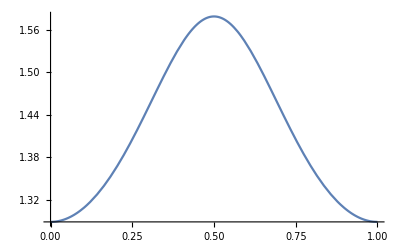

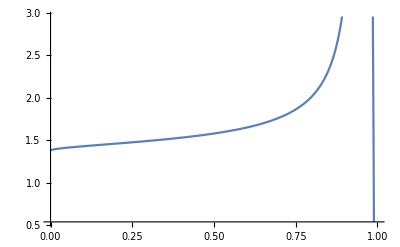

```mathematica
aaaReflectance[m_,inViewDir__,ϵ1_,ϵ2_]:=Block[
	{aaa},
	
	aaa=gSamplingLightDir[m,inViewDir,ϵ1,ϵ2];
	aaa[[3]]
];
Plot[aaaReflectance[0.1,{1,0,1},0.5,ϵ2],{ϵ2,0,1}]
Plot[aaaReflectance[0.1,{1,0,1},ϵ1,0.5],{ϵ1,0,1}]
```

```mathematica
gSamplingLightDir[0.1,{1,0,1},0.3,0.3]
```

{{-0.735018,0.0859013,0.672584},5.67664,1.41805}

```mathematica
Integrate[(2 m^2 Cos[θ] Sin[θ])/((1+Cos[θ]^2 (-1+m^2) )^2)/.{m->0.3},{θ,0,π/2}]
```

1.

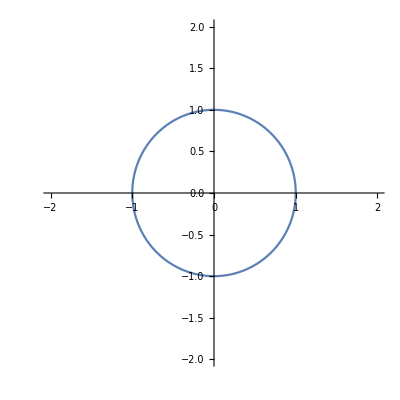

```mathematica
aaaFunc[m_,inViewDir_,θ_]:=Module[
{}

];
ParametricPlot[
		aaaFunc[0.1,{1,1},θ],
		{θ,0,2π},
		PlotRange->{{-2,2},{-2,2}},
		AspectRatio->1]
```